```mathematica
1+2
```

3

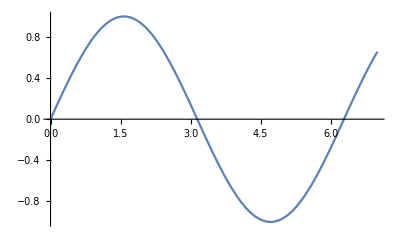

```mathematica
Plot[Sin[x],{x,0,7}]
```

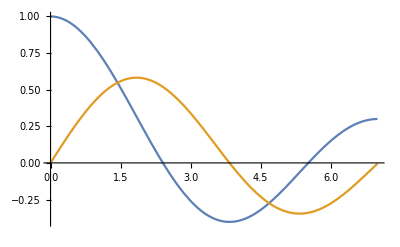

```mathematica
Plot[{BesselJ[0,x],BesselJ[1,x]},{x,0,7}]
```

```mathematica
f=Series[Exp[x],{x,0,8}]
```

1+x+x^2/2+x^3/6+x^4/24+x^5/120+x^6/720+x^7/5040+x^8/40320+O[x]^9

```mathematica
g=Normal[f]
```

1+x+x^2/2+x^3/6+x^4/24+x^5/120+x^6/720+x^7/5040+x^8/40320

## Patterns

Element extraction

```mathematica
g[[5]]
```

x^4/24

```mathematica
g⟦6⟧
```

x^5/120

```mathematica
gg=g/.{x->-x}
```

1-x+x^2/2-x^3/6+x^4/24-x^5/120+x^6/720-x^7/5040+x^8/40320

```mathematica
Simplify[(g+gg)/2]
```

1/2 (2+x^2+x^4/12+x^6/360+x^8/20160)

```mathematica
Expand[(g+gg)/2]
```

1+x^2/2+x^4/24+x^6/720+x^8/40320

```mathematica
g/.x^n_->0
```

1+x

```mathematica
Power[x,2]
```

x^2

```mathematica
g/.{x^n_/;OddQ[n]->0}
```

1+x+x^2/2+x^4/24+x^6/720+x^8/40320

```mathematica
IntegerQ[Sqrt[10]]
```

False

```mathematica
g/.{x^n_/;IntegerQ[Sqrt[n]]->0}
```

1+x+x^2/2+x^3/6+x^5/120+x^6/720+x^7/5040+x^8/40320

```mathematica
g
```

1+x+x^2/2+x^3/6+x^4/24+x^5/120+x^6/720+x^7/5040+x^8/40320

```mathematica
h=g/.x->y
```

1+y+y^2/2+y^3/6+y^4/24+y^5/120+y^6/720+y^7/5040+y^8/40320

```mathematica
g+h/.{x_^n_/;OddQ[n]||IntegerQ[Sqrt[n]]->0}
```

2+x+x^2/2+x^6/720+x^8/40320+y+y^2/2+y^6/720+y^8/40320

```mathematica
&&
```

```mathematica
||
```

```mathematica
(g/.{x^n_/;OddQ[n]->0})-x
```

1+x^2/2+x^4/24+x^6/720+x^8/40320

```mathematica
%/.x->I x
```

1-x^2/2+x^4/24-x^6/720+x^8/40320

```mathematica
h=%
```

1-x^2/2+x^4/24-x^6/720+x^8/40320

```mathematica
FullForm[h]
```

Plus[1,Times[Rational[-1,2],Power[x,2]],Times[Rational[1,24],Power[x,4]],Times[Rational[-1,720],Power[x,6]],Times[Rational[1,40320],Power[x,8]]]

```mathematica
Head[h]
```

Plus

```mathematica
Map[M,h]
```

M[1]+M[-x^2/2]+M[x^4/24]+M[-x^6/720]+M[x^8/40320]

```mathematica
Apply[M,h]
```

M[1,-x^2/2,x^4/24,-x^6/720,x^8/40320]

```mathematica
Apply[Times,h]
```

x^20/1393459200

```mathematica
A={{Cos[x],Sin[x]},{Sin[x],-Cos[x]}}
```

{{Cos[x],Sin[x]},{Sin[x],-Cos[x]}}

```mathematica
A//MatrixForm
```

(Cos[x] | Sin[x]
Sin[x] | -Cos[x])

```mathematica
A.A
```

{{Cos[x]^2+Sin[x]^2,0},{0,Cos[x]^2+Sin[x]^2}}

```mathematica
Simplify[A.A]//MatrixForm
```

(1 | 0
0 | 1)

```mathematica
Eigenvalues[A]
```

{-1,1}

```mathematica
Eigenvectors[A]
```

{{Cot[x]-Csc[x],1},{Cot[x]+Csc[x],1}}

```mathematica
MatrixExp[A t]
```

{{-1/2 ⅇ^-t (-1+Cos[x])+1/2 ⅇ^t (1+Cos[x]),-1/2 ⅇ^-t Sin[x]+1/2 ⅇ^t Sin[x]},{-1/2 ⅇ^-t Sin[x]+1/2 ⅇ^t Sin[x],-1/2 ⅇ^-t (-1-Cos[x])+1/2 ⅇ^t (1-Cos[x])}}

```mathematica
Simplify[MatrixExp[A t]]
```

{{1/2 ⅇ^-t (1-Cos[x]+ⅇ^(2 t) (1+Cos[x])),1/2 ⅇ^-t (-1+ⅇ^(2 t)) Sin[x]},{1/2 ⅇ^-t (-1+ⅇ^(2 t)) Sin[x],1/2 ⅇ^-t (1+ⅇ^(2 t)+Cos[x]-ⅇ^(2 t) Cos[x])}}

```mathematica
FullSimplify[MatrixExp[A t]]//MatrixForm
```

(Cosh[t]+Cos[x] Sinh[t] | Sin[x] Sinh[t]
Sin[x] Sinh[t] | Cosh[t]-Cos[x] Sinh[t])

```mathematica
f=.
g=.
```

```mathematica
f[x_]:=BesselJ[0,x]
g[x_]:=BesselJ[1,x]
```

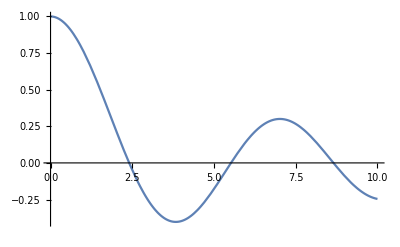

```mathematica
Plot[f[x],{x,0,10}]
```

```mathematica
∞
```

```mathematica
Series[f[x],{x,Infinity,1}]
```

Cos[π/4-x] (√(2/π) √(1/x)+O[1/x]^(3/2))+(-(1/x)^(3/2)/(4 √(2 π))+O[1/x]^2) Sin[π/4-x]

```mathematica
fn=Normal[%[[1]]]
```

√(2/π) √(1/x) Cos[π/4-x]

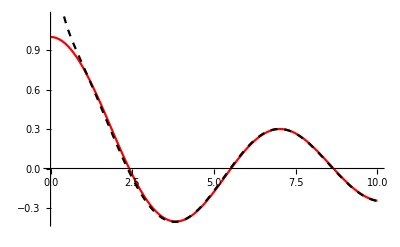

```mathematica
Plot[{f[x],fn},{x,0,10},PlotStyle->{Red,{Black,Dashed}}]
```

```mathematica
f[x_]:=BesselJ[0,x]
```

```mathematica
f1=BesselJ[0,#]&
```

BesselJ[0,#1]&

```mathematica
f1[7]
```

BesselJ[0,7]

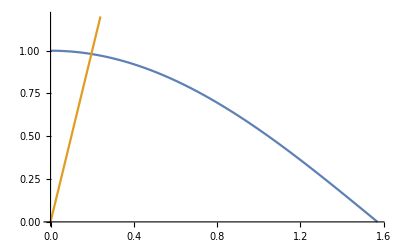

```mathematica
Plot[{Cos[x],5x},{x,0,Pi/2},PlotRange->{All,{0,1.2}}]
```

```mathematica
FindRoot[Cos[x]==5 x,{x,1}]
```

{x→0.196164}

```mathematica
FindRoot[Cos[x]== x,{x,1}]
```

{x→0.739085}

```mathematica
%[[1,2]]
```

0.739085

```mathematica
Pi
```

π

```mathematica
N[π,20]
```

3.1415926535897932385

```mathematica
Φ=.
```

```mathematica
Remove[Φ]
```

```mathematica
Φ[t_?NumericQ]:=x/.FindRoot[Cos[x]==t x,{x,1}]
```

```mathematica
Φ[1]
```

0.739085

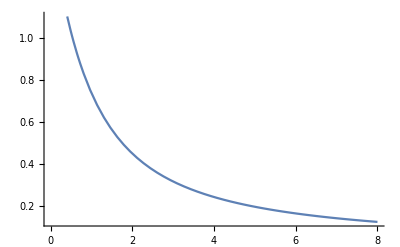

```mathematica
Plot[Φ[x],{x,0,8}]
```

```mathematica
NIntegrate[Φ[z],{z,0,1}]
```

1.0697

```mathematica
Ψ[y_]:=NIntegrate[Φ[x],{x,0,y}]
```

```mathematica
Ψ[1]
```

0.824132

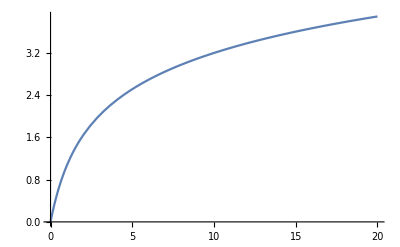

```mathematica
Plot[Ψ[z],{z,0,20}]
```

```mathematica
NIntegrate[z^3,{z,0,1}]
```

0.25

```mathematica
z
```

z

```mathematica
D[Sqrt[Sin[x]],x]
```

Cos[x]/(2 √Sin[x])

```mathematica
D[Sqrt[Sin[x]],{x,2}]
```

-Cos[x]^2/(4 Sin[x]^(3/2))-(√Sin[x])/2

```mathematica
Integrate[Exp[-a x],x]
```

-ⅇ^(-a x)/a

```mathematica
Integrate[Exp[-a x],{x,0,1}]
```

(1-ⅇ^-a)/a

```mathematica
Integrate[Exp[-a x^6],x]
```

-(x Gamma[1/6,a x^6])/(6 (a x^6)^(1/6))

```mathematica
Integrate[BesselJ[0,x]Exp[-a x^6],x]
```

∫ⅇ^(-a x^6) BesselJ[0,x]ⅆx

```mathematica
Integrate[Exp[-a x],{x,0,∞}]
```

ConditionalExpression[1/a,Re[a]>0]

```mathematica
Integrate[Exp[-a x],{x,0,∞},Assumptions->{a>0}]
```

1/a

```mathematica
Integrate[Cos[x]/(1+x^2),{x,-∞,∞}]
```

π/ⅇ

```mathematica
Integrate[Cos[x]/(1+x^2),{x,-∞,∞}]
```

π/ⅇ

```mathematica
Integrate[Cos[x]/(a^2+x^2),{x,-∞,∞}]
```

ConditionalExpression[(ⅇ^-a π)/a,Re[a]>0]

```mathematica
Integrate[Exp[I q r Cos[ϕ]]/(2π),{ϕ,0,2π}]
```

ConditionalExpression[BesselJ[0,q r],q r∈Reals]

```mathematica
Integrate[BesselJ[0,q r] q/(q^2+κ^2),{q,0,∞}]
```

ConditionalExpression[BesselK[0,r/(√(1/κ^2))],Im[r]==0&&(Re[κ^2]≥0||κ^2∉Reals)&&Re[r]>0]

```mathematica
Integrate[BesselJ[0,q r] q/(q^2+κ^2),{q,0,∞},Assumptions->{r>0,κ>0}]
```

BesselK[0,r κ]

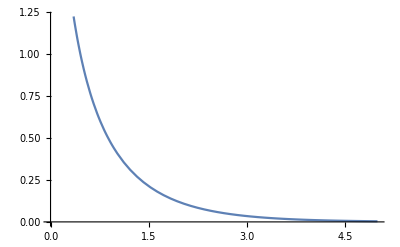

```mathematica
Plot[BesselK[0,x],{x,0,5}]
```

```mathematica
Series[BesselK[0,x],{x,0,0}]
```

(-EulerGamma+Log[2]-Log[x])+O[x]^1

```mathematica
R[m_,n_]:=Integrate[(1-Cos[m x+n y])/(2-Cos[x]-Cos[y]),{x,0,2π},{y,0,2π}]/(2π)^2
```

```mathematica
Timing[R[1,0]]
```

{6.0493,1/2}

```mathematica
Timing[R[1,1]]
```

{23.87568,2/π}

```mathematica
Timing[Expand[R[2,0]]]
```

{0.89897,2-4/π}

```mathematica
Timing[Expand[R[3,0]]]
```

{2.31089,17/2-24/π}

```mathematica
Timing[Expand[R[2,1]]]
```

{24.88875,-1/2+4/π}

```mathematica
NIntegrate[(1-Cos[100 x])/(2-Cos[x]-Cos[y]),{x,0,2π},{y,0,2π}]/(2π)^2
```

1.98056

```mathematica
NIntegrate[(1-Cos[1000 x])/(2-Cos[x]-Cos[y]),{x,0,2π},{y,0,2π}]/(2π)^2
```

2.71349

```mathematica
NIntegrate[1/(3-Cos[x]-Cos[y]-Cos[z]),{x,0,2π},{y,0,2π},{z,0,2π}]/(2π)^3
```

0.505462